```mathematica
(* MA39110 / Assignment 3 / 16MA20053 / NER ROHIT *)
ClearAll["Global`*"];
```

```mathematica
BlockThomas[a_, b_, c_, d_]:=Module[{b1=Array[0&,{Length[b],1,2,2}],c1=Array[0&,{Length[c],1,2,2}],d1=Array[0&,{Length[d],1,2,1}],x=Array[0&,{Length[b],1,2,1}]},
c1[[1,1]]=Dot[Inverse[b[[1,1]]],c[[1,1]]]; d1[[1,1]]=Dot[Inverse[b[[1,1]]],d[[1,1]]];
Do[
b1[[i,1]]=b[[i,1]]-Dot[a[[i-1,1]],c1[[i-1,1]]];
If[i≠Length[d],c1[[i,1]]=Dot[Inverse[b1[[i,1]]],c[[i,1]]];];
d1[[i,1]]=Dot[Inverse[b1[[i,1]]],d[[i,1]]-Dot[a[[i-1,1]],d1[[i-1,1]]]];
,{i,2,Length[d]}];
x[[Length[b],1]]=d1[[Length[b],1]];
Do[
x[[i,1]]=d1[[i,1]]-Dot[c1[[i,1]],x[[i+1,1]]];
,{i,Length[b]-1,1,-1}];
x];
```

```mathematica
Model[n0_]:=Module[{n=n0},
x0=0;xf=1;h=(xf-x0)/n;
a=Array[{{0,0},{0,0}}&,{n-2,1}];
b=Array[{{0,0},{0,0}}&,{n-1,1}];
c=Array[{{0,0},{0,0}}&,{n-2,1}];
d=Array[{0,0}&,{n-1,1}];
X=Table[x0+x*h,{x,1,n-1}];
For[i=1,i<=n-1,i++,
{
b[[i,1]]={{-2/h^2,-1},{81,-2/h^2}};
d[[i,1]]={0,81*X[[i]]^2};
If[i≠n-1,{a[[i,1]]={{1/h^2,0},{0,1/h^2}},c[[i,1]]={{1/h^2,0},{0,1/h^2}}}];
}];
N[Flatten[BlockThomas[a,b,c,d]][[1;;;;2]]]];
```

```mathematica
in={25,30,40};
sol=Model[in[[1]]];
solt=DSolve[{y''''[x]+81y[x]==81x^2,y[0]==y[1]==y''[0]==y''[1]==0},y[x],x];
err1=Abs[DSolveValue[{y''''[x]+81y[x]==81x^2,y[0]==y[1]==y''[0]==y''[1]==0},y[X],x]-sol];
perr1 = ListPlot[Transpose[{X,err1}],PlotStyle->Red];
N[Max[err1]]
p1=Show[{Plot[Evaluate[y[x]/.solt],{x,x0,xf},PlotLabel->Style[StringForm["h = ``",N[h]],FontSize->18]]},{ListPlot[Transpose[{X,sol}],PlotStyle->Red]}];
```

0.000176946

```mathematica
sol=Model[in[[2]]];
solt=DSolve[{y''''[x]+81y[x]==81x^2,y[0]==y[1]==y''[0]==y''[1]==0},y[x],x];
err2=Abs[DSolveValue[{y''''[x]+81y[x]==81x^2,y[0]==y[1]==y''[0]==y''[1]==0},y[X],x]-sol];
perr2 = ListPlot[Transpose[{X,err2}],PlotStyle->Green];
N[Max[err2]]
p2=Show[{Plot[Evaluate[y[x]/.solt],{x,x0,xf},PlotLabel->Style[StringForm["h = ``",N[h]],FontSize->18]]},{ListPlot[Transpose[{X,sol}],PlotStyle->Red]}];
```

0.000122922

```mathematica
sol=Model[in[[3]]];
solt=DSolve[{y''''[x]+81y[x]==81x^2,y[0]==y[1]==y''[0]==y''[1]==0},y[x],x];
err3=Abs[DSolveValue[{y''''[x]+81y[x]==81x^2,y[0]==y[1]==y''[0]==y''[1]==0},y[X],x]-sol];
perr3 = ListPlot[Transpose[{X,err3}],PlotStyle->Blue];
N[Max[err3]]
p3=Show[{Plot[Evaluate[y[x]/.solt],{x,x0,xf},PlotLabel->Style[StringForm["h = ``",N[h]],FontSize->18]]},{ListPlot[Transpose[{X,sol}],PlotStyle->Red]}];
```

0.0000691074

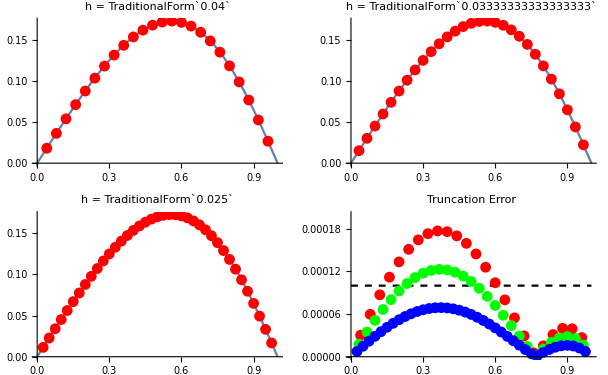

```mathematica
p4=Show[{Plot[y[x]=10^-4,{x,0,1},PlotStyle->{Dashed,Black}]},{perr1},{perr2},{perr3},PlotLabel->Style["Truncation Error",FontSize->18],PlotRange->{{0,1},{0,0.0002}}];
GraphicsGrid[{{p1,p2},{p3,p4}}]
```